## Creating figures

Hello and welcome. In this lecture we will look at how to create figures.

### Introduction

In a previous lecture we saw how we can model a pendulum.

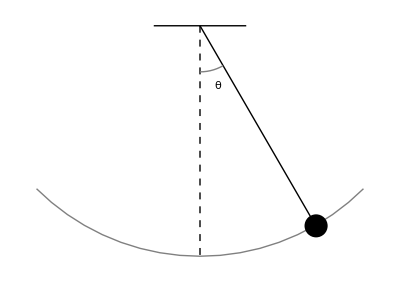

In this lecture, we’ll see how we can draw that figure. So this lecture will cover a lot of graphics stuff.

Mathematica has a very powerful graphics engine, and it has many different primitive graphics types. These graphics types allow us to draw things. One of the primitives that we can take a look at is Line. Line of course allows us to draw a line.

```mathematica
?Line
```

Line[{p_1,p_2,…}] represents the line segments joining a sequence for points p_i.
Line[{{p_11,p_12,…},{p_21,…},…}] represents a collection of lines.

We also have Circle, which enables us to draw a circle.

```mathematica
?Circle
```

Circle[{x,y},r] represents a circle of radius r centered at {x,y}.
Circle[{x,y}] gives a circle of radius 1. 
Circle[{x,y},{r_x,r_y}] gives an axis-aligned ellipse with semi-axes lengths r_x and r_y.
Circle[{x,y},…,{θ_1,θ_2}] gives a circular or ellipse arc from angle θ_1 to θ_2.

We also have Disk.

```mathematica
?Disk
```

Disk[{x,y},r] represents a disk of radius r centered at {x,y}.
Disk[{x,y}] gives a disk of radius 1. 
Disk[{x,y},{r_x,r_y}] gives an axis-aligned elliptical disk with semiaxes lengths r_x and r_y.
Disk[{x,y},…,{θ_1,θ_2}] gives a sector of a disk from angle θ_1 to θ_2.

### Drawing the Pendulum

We are going to be using these to draw our pendulum figure. In order to draw a line, or a circle, or a disk, we need to pass these objects to a function called Graphics. Graphics takes a set of graphic primitives and displays them.

```mathematica
?Graphics
```

Graphics[primitives,options] represents a two-dimensional graphical image.

So let’s draw a line.

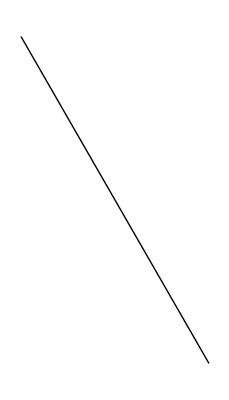

```mathematica
Graphics[Line[{{0,0},{Cos[Pi/3],-Sin[Pi/3]}}],ImageSize->Tiny]
```

Let’s make it a bit smaller. And let’s draw the horizontal line now. Let’s put our graphic primitives into a list. And we are going to put each of our graphic primitives on a line to make it easier to read.

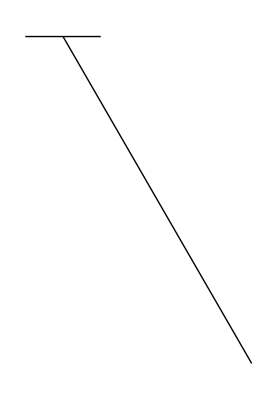

```mathematica
Graphics[{
Line[{{0,0},{Cos[Pi/3],-Sin[Pi/3]}}],
Line[{{-0.1,0},{0.1,0}}]
},ImageSize->Tiny]
```

So now we have the point where the pendulum attaches. Next let’s draw the disk here. The disk needs to be centered at the end point of the line.

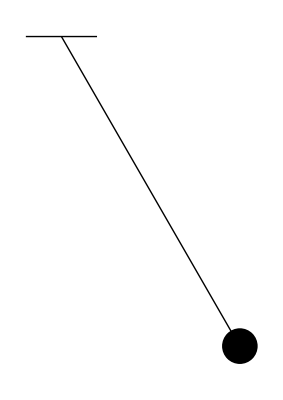

```mathematica
Graphics[{
Line[{{0,0},{Cos[Pi/3],-Sin[Pi/3]}}],
Line[{{-0.1,0},{0.1,0}}],
Disk[{Cos[Pi/3],-Sin[Pi/3]},0.05]
},ImageSize->Tiny]
```

Let’s take a look at where we are. We only have a few more things to do. Let’s start with the y-axis.

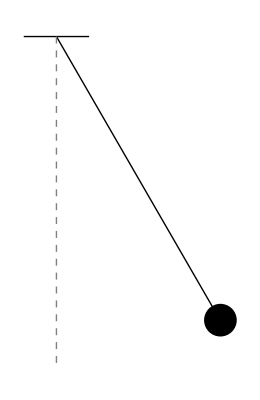

```mathematica
Graphics[{
Line[{{0,0},{Cos[Pi/3],-Sin[Pi/3]}}],
Line[{{-0.1,0},{0.1,0}}],
Disk[{Cos[Pi/3],-Sin[Pi/3]},0.05],
{Dashed,Gray,Line[{{0,0},{0,-1}}]}
},ImageSize->Tiny]
```

Next we have to do the arc. This will be a circle, but we will only draw a portion of it. It will be centered at the point (0,0). As we saw with the disk, it took up the entire picture. So if we want this circle to work correctly, we want it to have a radius of 1.

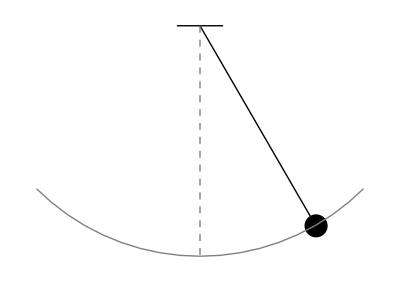

```mathematica
Graphics[{
Line[{{0,0},{Cos[Pi/3],-Sin[Pi/3]}}],
Line[{{-0.1,0},{0.1,0}}],
Disk[{Cos[Pi/3],-Sin[Pi/3]},0.05],
{Dashed,Gray,Line[{{0,0},{0,-1}}]},
{Gray,Circle[{0,0},1,{-3Pi/4,-Pi/4}]}
},ImageSize->Tiny]
```

The next thing is the tiny arc that represent our θ variable.

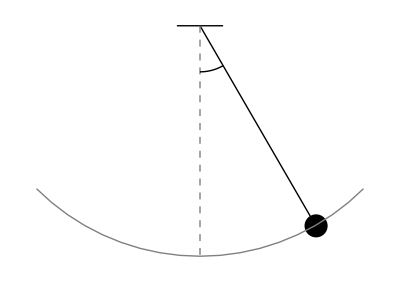

```mathematica
Graphics[{
Line[{{0,0},{Cos[Pi/3],-Sin[Pi/3]}}],
Line[{{-0.1,0},{0.1,0}}],
Disk[{Cos[Pi/3],-Sin[Pi/3]},0.05],
{Dashed,Gray,Line[{{0,0},{0,-1}}]},
{Gray,Circle[{0,0},1,{-3Pi/4,-Pi/4}]},
Circle[{0,0},.2,{-Pi/2,-Pi/3}]
},ImageSize->Tiny]
```

The last thing to do is to put the symbol θ there. Text in Mathematica is just a string. We need to take that text and convert it into a graphics object. So the Text object is a primitive graphic type that will help us do that.

```mathematica
?Text
```

Text[expr] displays with expr in plain text format. 
Text[expr,coords] is a graphics primitive that displays the textual form of expr centered at the point specified by coords.

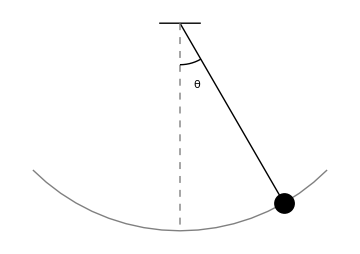

```mathematica
Graphics[{
Line[{{0,0},{Cos[Pi/3],-Sin[Pi/3]}}],
Line[{{-0.1,0},{0.1,0}}],
{Dashed,Gray,Line[{{0,0},{0,-1}}]},
{Gray,Circle[{0,0},1,{-3Pi/4,-Pi/4}]},
Circle[{0,0},.2,{-Pi/2,-Pi/3}],
{FontSize->18,Text["θ",{0.08,-0.3}]},
Disk[{Cos[Pi/3],-Sin[Pi/3]},0.05]
},ImageSize->Medium]
```

### Other Graphics Primitives

Mathematica also provides many other graphic primitives beyond the ones I’ve shown you just now, including Polygon.

```mathematica
?Polygon
```

Polygon[{p_1,…,p_n}] represents a filled polygon with points p_i.
Polygon[{{p_11,…},{p_21,…},…}] represents a collection of polygons.

Polygon allows us to draw a sequence of points and then fill it.

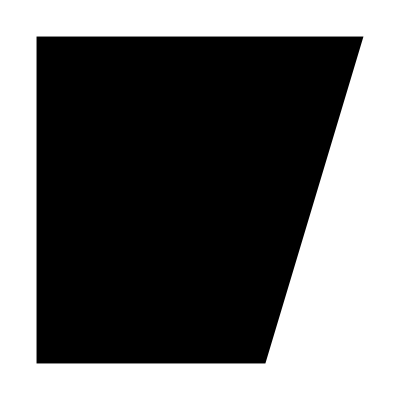

```mathematica
Graphics[Polygon[{{0,0},{0.7,0},{1,1},{0,1}}],ImageSize->Tiny]
```

Other simple things include the Rectangle. This graphics primitive allows us to draw rectangles. \\

```mathematica
?Rectangle
```

Rectangle[{x_min,y_min},{x_max,y_max}] represents an axis-aligned filled rectangle from {x_min,y_min} to {x_max,y_max}.
Rectangle[{x_min,y_min}] corresponds to a unit square with its bottom-left corner at {x_min,y_min}.

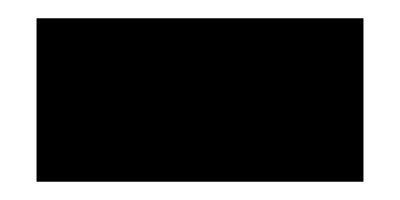

```mathematica
Graphics[Rectangle[{0,0},{2,1}],ImageSize->Tiny]
```

Mathematica also provides triangles, many different types of triangles in fact. We’ll just take a look at one of them.

```mathematica
?Triangle
```

Triangle[{p_1,p_2,p_3}] represents a filled triangle with corner points p_1, p_2, and p_3.
Triangle[{{p_11,p_12,p_13},…}] represents a collection of triangles.

So here we just give it the three points of the triangle.



```mathematica
Graphics[Triangle[{{0,0},{1,0},{0.5,Sqrt[3]/2}}],ImageSize->Tiny]
```

So far we’ve seen only these black objects. Maybe we could style these a little bit. Let’s take our triangle and add color to it.

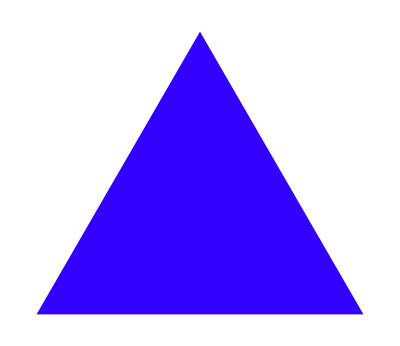

```mathematica
Graphics[{RGBColor[0.2,0,4],Triangle[{{0,0},{1,0},{0.5,Sqrt[3]/2}}]},ImageSize->Tiny]
```

This is the first time we’ve seen RGBColor used. So far we’ve only ever used named colors.

```mathematica
?RGBColor
```

RGBColor[red,green,blue] is a graphics directive specifying that objects that follow are to be displayed in the color given. 
RGBColor[r,g,b,a] specifies opacity a. 
RGBColor[string] evaluates to a normal RGBColor object.

Let’s take a look at tracing the object, giving it a border. We will use the function called EdgeForm.

```mathematica
?EdgeForm
```

EdgeForm[g] is a graphics directive which specifies that edges of polygons and other filled graphics objects are to be drawn using the graphics directive or list of directives g.

We put the EdgeForm in the same way that we have RGBColor into the graphics primitive, and it will use that as the style of the edge.

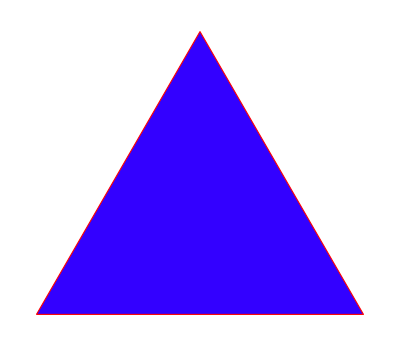

```mathematica
Graphics[{EdgeForm[{Red,Dashed,Thick}],RGBColor[0.2,0,4],Triangle[{{0,0},{1,0},{0.5,Sqrt[3]/2}}]},ImageSize->Tiny]
```

Let’s go back and take a look at Opacity. In order to do that, we’ll need two objects in our graphcis view.

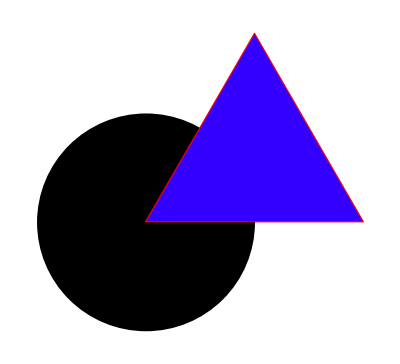

```mathematica
Graphics[{
Disk[{0,0},0.5],
{EdgeForm[{Red,Dashed,Thick}],RGBColor[0.2,0,4],Triangle[{{0,0},{1,0},{0.5,Sqrt[3]/2}}]}
},ImageSize->Tiny]
```

How can we make our triangle semitransparent? We do this using Opacity.

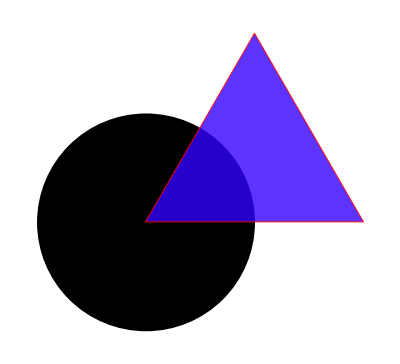

```mathematica
Graphics[{
Disk[{0,0},0.5],
{Opacity[0.8],EdgeForm[{Red,Dashed,Thick}],RGBColor[0.2,0,4],Triangle[{{0,0},{1,0},{0.5,Sqrt[3]/2}}]}
},ImageSize->Tiny]
```

Now you can see the disk is visible through the triangle. Another way of doing the Opacity is by putting it in the RGBColor.

```mathematica
Graphics[{
Disk[{0,0},0.5],
{EdgeForm[{Red,Dashed,Thick}],RGBColor[0.2,0,4,0.8],Triangle[{{0,0},{1,0},{0.5,Sqrt[3]/2}}]}
},ImageSize->Tiny]
```

### Summary

This covers our little tutorials on graphics in Mathematica. You can use it to make all kinds of graphics, and later we’ll use what we’ve learned here to do animations. I hope you had fun. I’ll see you next time.